```mathematica
eq1 = g[t] == m1*x1''[t]  + k1 *(x1[t])  - k2*(x2[t] - x1[t]) + b1*(x1'[t]) + b2*(x1'[t]-x2'[t]);
eq2 = m2 *x2''[t] == -k2*(x2[t] - x1[t]) - b2*(x2'[t]-x1'[t]);
```

```mathematica
L1 = LaplaceTransform[eq1, t, s](*/.{x1[0]-> 0, x2[0]-> 0, x1'[0]-> 0, x2'[0]-> 0, k1-> 5, k2-> 5, b1 ->5, b2->5, m1 -> 2, m2 ->2};*)
L2 = LaplaceTransform[eq2, t, s](*/.{x1[0]-> 0, x2[0]-> 0, x1'[0]-> 0, x2'[0]-> 0, k1-> 5, k2-> 5, b1 ->5, b2->5, m1 -> 2, m2 ->2};*)

X1 = Solve[L2,LaplaceTransform[x1[t],t,s]]


sol = Solve[L1/.X1,LaplaceTransform[g[t],t,s]]

Collect[sol,LaplaceTransform[x2[t],t,s]] /.{x1[0]-> 0, x2[0]-> 0, x1'[0]-> 0, x2'[0]-> 0, k1-> 5, k2-> 5, b1 ->5, b2->5, m1 -> 2, m2 ->2}
```

LaplaceTransform[g[t],t,s]==k1 LaplaceTransform[x1[t],t,s]+k2 LaplaceTransform[x1[t],t,s]-k2 LaplaceTransform[x2[t],t,s]+b1 (s LaplaceTransform[x1[t],t,s]-x1[0])+b2 (s LaplaceTransform[x1[t],t,s]-x1[0])-b2 (s LaplaceTransform[x2[t],t,s]-x2[0])+m1 (s^2 LaplaceTransform[x1[t],t,s]-s x1[0]-x1'[0])

m2 (s^2 LaplaceTransform[x2[t],t,s]-s x2[0]-x2'[0])==k2 LaplaceTransform[x1[t],t,s]-k2 LaplaceTransform[x2[t],t,s]+b2 (s LaplaceTransform[x1[t],t,s]-x1[0])-b2 (s LaplaceTransform[x2[t],t,s]-x2[0])

{{LaplaceTransform[x1[t],t,s]→(k2 LaplaceTransform[x2[t],t,s]+b2 s LaplaceTransform[x2[t],t,s]+m2 s^2 LaplaceTransform[x2[t],t,s]+b2 x1[0]-b2 x2[0]-m2 s x2[0]-m2 x2'[0])/(k2+b2 s)}}

{{LaplaceTransform[g[t],t,s]→1/(k2+b2 s)(k1 k2 LaplaceTransform[x2[t],t,s]+b2 k1 s LaplaceTransform[x2[t],t,s]+b1 k2 s LaplaceTransform[x2[t],t,s]+b1 b2 s^2 LaplaceTransform[x2[t],t,s]+k2 m1 s^2 LaplaceTransform[x2[t],t,s]+k1 m2 s^2 LaplaceTransform[x2[t],t,s]+k2 m2 s^2 LaplaceTransform[x2[t],t,s]+b2 m1 s^3 LaplaceTransform[x2[t],t,s]+b1 m2 s^3 LaplaceTransform[x2[t],t,s]+b2 m2 s^3 LaplaceTransform[x2[t],t,s]+m1 m2 s^4 LaplaceTransform[x2[t],t,s]+b2 k1 x1[0]-b1 k2 x1[0]-k2 m1 s x1[0]-b2 k1 x2[0]-b1 b2 s x2[0]-k1 m2 s x2[0]-k2 m2 s x2[0]-b2 m1 s^2 x2[0]-b1 m2 s^2 x2[0]-b2 m2 s^2 x2[0]-m1 m2 s^3 x2[0]-k2 m1 x1'[0]-b2 m1 s x1'[0]-k1 m2 x2'[0]-k2 m2 x2'[0]-b1 m2 s x2'[0]-b2 m2 s x2'[0]-m1 m2 s^2 x2'[0])}}

{{LaplaceTransform[g[t],t,s]→((25+50 s+55 s^2+30 s^3+4 s^4) LaplaceTransform[x2[t],t,s])/(5+5 s)}}

```mathematica
Transfer = 1/((25+50 s+55 s^2+30 s^3+4 s^4)/(5 +5s))

transferfunc[w] = Transfer/.{s-> Sqrt[-1]*w}
```

(5+5 s)/(25+50 s+55 s^2+30 s^3+4 s^4)

(5+5 ⅈ w)/(25+50 ⅈ w-55 w^2-30 ⅈ w^3+4 w^4)

```mathematica
Plot[{Tooltip@Re@transferfunc[w],Tooltip@Im@transferfunc[w]},{w,-10,10},PlotStyle->Thick,PlotRange->All]
```

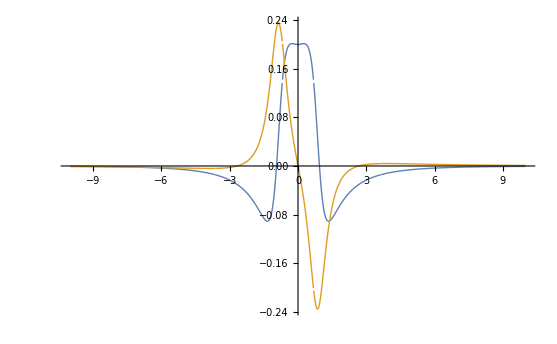
```mathematica
-Graphics-LinguisticAssistant
```